## Example 1, advection equation with c = 4 and initial condition arctan(x)

### Characteristic lines

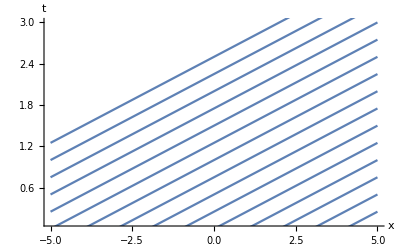

```mathematica
Show[
{Plot[Table[(x-x0)/4,{x0,-10,5}],{x,-5,5}]},
PlotRange->{0.1,3},AxesLabel->{"x","t"}, AxesStyle->Large
]
```

### Initial condition

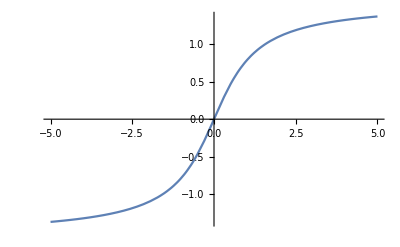

```mathematica
Plot[ArcTan[x],{x,-5,5}]
```

### The solution

```mathematica
Plot3D[ArcTan[x-4t],{x,-5,5},{t,0,1},ColorFunction->"TemperatureMap", AxesStyle->Large,AxesLabel->{"x","t"}, PlotLegends->Automatic,PlotRange->{-2,2}]
```

-Graphics3D-

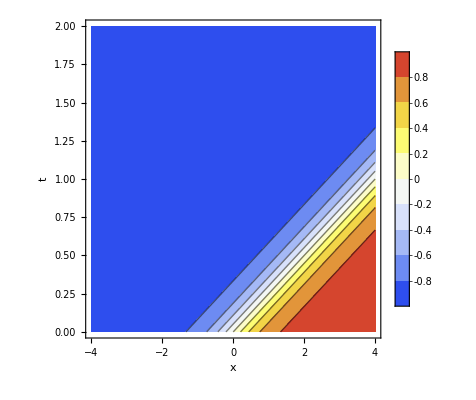

```mathematica
ContourPlot[
Sin[ArcTan[x-4t]],{x,-4,4},{t,0,2},ColorFunction->"TemperatureMap", AxesStyle->Large,AxesLabel->{"x","t"}, PlotLegends->Automatic,PlotRange->{-1,1}]
```

## Example 2, advection equation with forcing f=t, with c = 4 and initial condition arctan(x)

### Characteristic lines

```mathematica
Show[
{Plot[Table[(x-x0)/4,{x0,-10,5}],{x,-5,5}]},
PlotRange->{0.1,3},AxesLabel->{"x","t"}, AxesStyle->Large
]
```

-Graphics-

### Initial condition

```mathematica
Plot[ArcTan[x],{x,-5,5}]
```

-Graphics-

### The solution

```mathematica
Plot3D[t^2/2+ArcTan[x-4t],{x,-5,5},{t,0,2},ColorFunction->"TemperatureMap", AxesStyle->Large,AxesLabel->{"x","t"}, PlotLegends->Automatic,PlotRange->{-2,2}]
```

-Graphics3D-

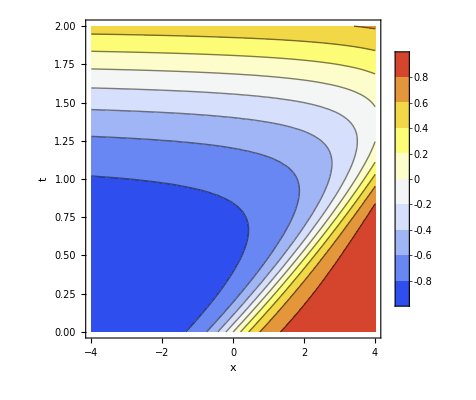

```mathematica
ContourPlot[
Sin[t^2/2+ArcTan[x-4t]],{x,-4,4},{t,0,2},ColorFunction->"TemperatureMap", AxesStyle->Large,AxesLabel->{"x","t"}, PlotLegends->Automatic,PlotRange->{-1,1}]
```

## Example 3, general linear conservation law, u_t + xu_x = 1, u(x,0) = 1/(1+x^4)

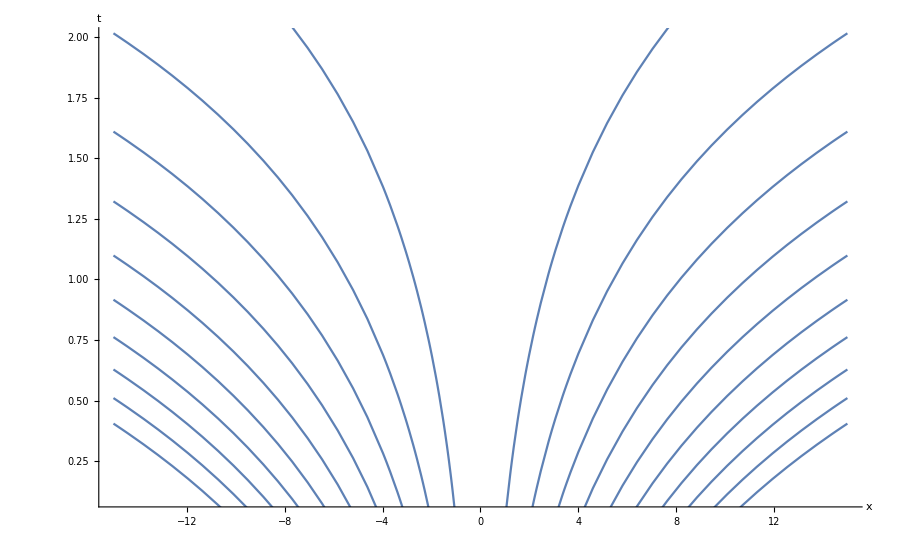

```mathematica
Show[
{Plot[Table[Log[x/x0],{x0,1,10}],{x,-15,15}],
Plot[Table[Log[x/x0],{x0,-10,-1}],{x,-15,15}]},
PlotRange->{0.1,2},AxesLabel->{"x","t"},AxesStyle->Large
]
```

```mathematica
Plot3D[
t + 1/(1+(x*Exp[-t])^4),{x,-10,10},{t,0,3},ColorFunction->"TemperatureMap",PlotLegends->Automatic,AxesLabel->{"x","t"}, AxesStyle->Large
]
```

-Graphics3D-

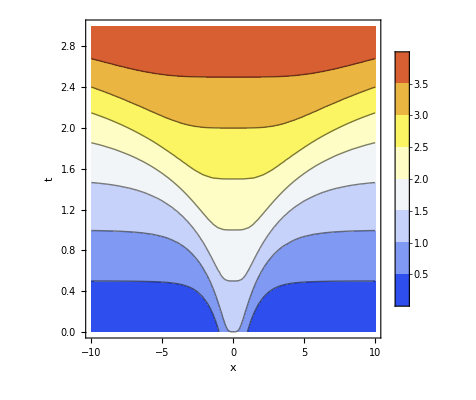

```mathematica
ContourPlot[t + 1/(1+(x*Exp[-t])^4),{x,-10,10},{t,0,3},ColorFunction->"TemperatureMap",PlotLegends->Automatic,AxesLabel->{"x","t"}, AxesStyle->Large
]
```

## Example 4, Burger’s equation with weird IC

### First let’s plot the IC

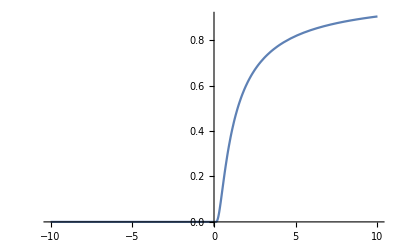

```mathematica
Plot[Piecewise[{{0,x≤0},{Exp[-1/x],x>0}}],{x,-10,10}]
```

### Plot the characteristics

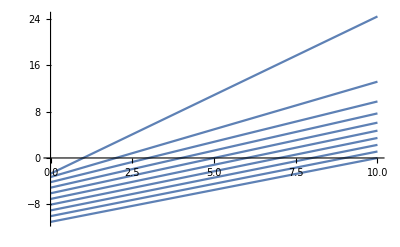

```mathematica
Plot[Table[Exp[1/x0](x-x0),{x0,1,10}],{x,0,10}]
```

## Example 5, Burgers equation with +arctan IC

### First plot the IC

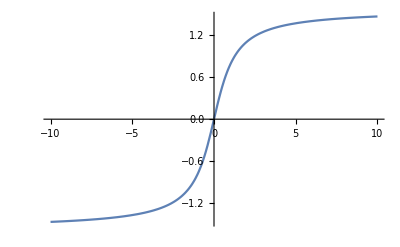

```mathematica
Plot[ArcTan[x],{x,-10,10}]
```

### Plot the characteristic curves

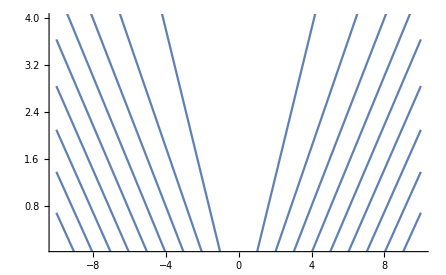

```mathematica
Show[
{Plot[
Table[(x-x0)/ArcTan[x0],{x0,1,10}],{x,-10,10}],
Plot[Table[(x-x0)/ArcTan[x0],{x0,-10,-1}],{x,-10,10}]},
PlotRange->{0.1,4}
]
```

## Example 6, Burgers equation with -arctan IC -- Catastrophe Gradients!

### First plot the IC

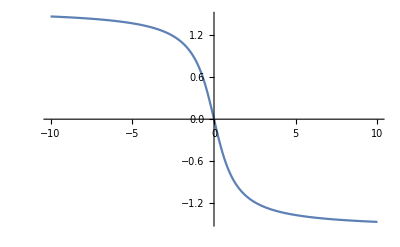

```mathematica
Plot[-ArcTan[x],{x,-10,10}]
```

### Plot the characteristic curves

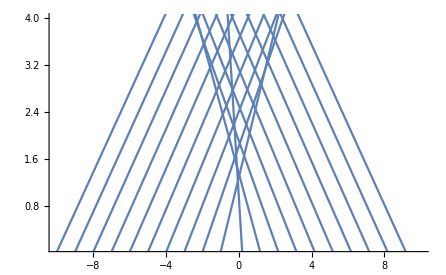

```mathematica
Show[
{Plot[
Table[-(x-x0)/ArcTan[x0],{x0,0.2,10}],{x,-10,10}],
Plot[Table[-(x-x0)/ArcTan[x0],{x0,-10,-0.2}],{x,-10,10}]},
PlotRange->{0.1,4}
]
```

## Example 7, Burgers equation with e^{-x^2} IC -- Find Breaking Time

### First plot the IC

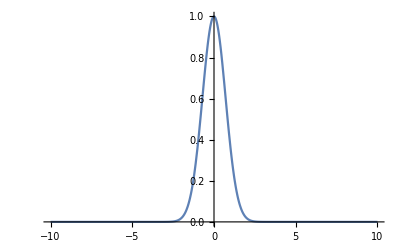

```mathematica
Plot[Exp[-x^2],{x,-10,10},PlotRange->{0,1}]
```

### Plot the characteristic curves

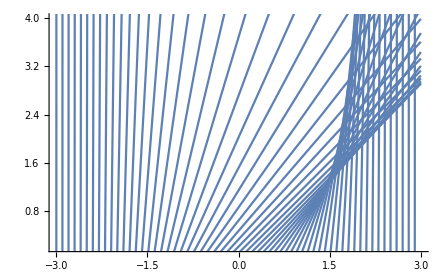

```mathematica
Show[
{Plot[
Table[(x-x0)*Exp[x0^2],{x0,-3,3,0.1}],{x,-3,3}]},
PlotRange->{0.2,4}
]
```

### Label the special characteristic and breaking time.

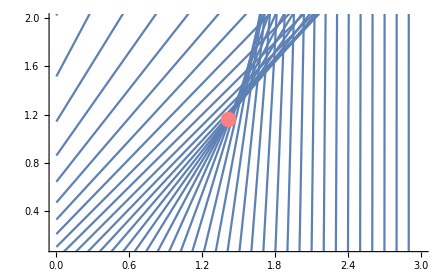

```mathematica
Show[
{Plot[
Table[(x-x0)*Exp[x0^2],{x0,-3,3,0.1}],{x,0,3}],
Graphics[{PointSize[0.025],Pink,Point[{1/Sqrt[2]+Sqrt[Exp[1]/2]*Exp[-1/2],Sqrt[Exp[1]/2]}]}]},
PlotRange->{0.1,2}
]
```

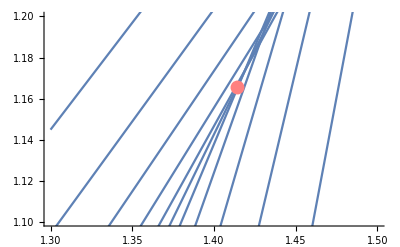

```mathematica
Show[
{Plot[
Table[(x-x0)*Exp[x0^2],{x0,-3,3,0.1}],{x,1.3,1.5}],
Graphics[{PointSize[0.025],Pink,Point[{1/Sqrt[2]+Sqrt[Exp[1]/2]*Exp[-1/2],Sqrt[Exp[1]/2]}]}]},
PlotRange->{1.1,1.2},Axes->True
]
```

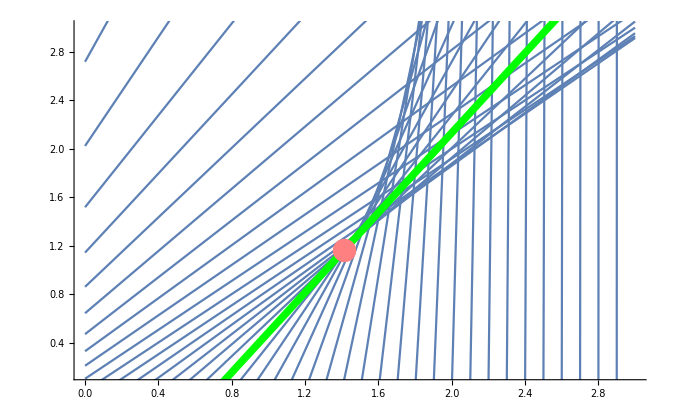

```mathematica
Show[
{Plot[
Table[(x-x0)*Exp[x0^2],{x0,-2,3,0.1}],{x,0,3}],
Plot[(x-1/Sqrt[2])*Exp[1/2],{x,0,3},PlotStyle->Directive[{Green,Thickness[0.008]}]],
Graphics[{PointSize[0.025],Pink,Point[{1/Sqrt[2]+Sqrt[Exp[1]/2]*Exp[-1/2],Sqrt[Exp[1]/2]}]}]},
PlotRange->{0.15,3}
]
```